# Constructing the secular Hamiltonian

## Evaluating integrals of multi-pole terms

Here I consider the secular evolution of a test particle interior to a (possibly eccentric) perturber, p. The Hamiltonian governing secular interactions is given by the “double-averaged” potential:
	ℋ_sec= -1/(4 π^2)(∫_0)^(2π)ⅆl(∫_0)^(2π)ⅆ l_p(G m_p)/(|r-r_p|)
	= -(G m_p)/(4 π^2 a_p)(∫_0)^(2π)ⅆl(∫_0)^(2π)ⅆ l_p  (∑_(j=2))^∞ α^j (r/a)^j(a_p/r_p)^(j+1)P_j[cos(Φ)]
where the second line gives the multi-pole expansion of  the potential in Legendre polynomials. 

I will use a coordinate system in which the x-y plane is the orbital plane of the perturber and the x direction is towards the pericenter of the perturber. In this coordinate system
	cos[Φ] = 1/(1-e_p cos[u_p])(cos[u_p]-e_p,√(1-e_p^2)sin[u_p],0)·(X,Y,Z)
	 =(1-e_p cos[u_p])^-1[(cos[u_p]-e_p)X + √(1-e_p^2)sin[u_p]Y]
where u_p is the perturber’s eccentric anomaly and (X,Y,Z) are the coordinates of the test particle’s position unit vector (explicit expressions to be given below.)

Integral of l_p

Integration over l_p can be done as follow:
	- First we will use ⅆ l_p=(1-e_p cos[u_p])ⅆ u_pto do the integral over eccentric anomaly

	- Note that r_p/a_p=1-e_p cos[u_p]

	- From the expression for cos[Φ] it is clear that the integrand is a series of terms of the form:
		(1-e cos[u_p])^-n cos^k_c[u_p]sin^k_s[u_p]

	- If k_s is odd then the integrand term is an odd function and its integral=0.  

	- If k_s is even, make the replacement sin[u_p]^2=1-cos[u_p]^2. Thus, all non-zero integrand terms can be expressed in the form:
		 (1-e cos[u_p])^-n cos^k[u_p]

Defining 
	 I_(n,k)(a,e)=1/(2π)(∫_0)^(2π)ⅆu  (a-e cos[u])^-n cos[u]^k
the recursion relations:
	 I_(1,0)(a,e)=1/(√(a^2-e^2))
I_(n,0)(a,e)=-1/(n-1)ⅆ/ⅆa I_(n-1,0)(a,e)
I_(n,k)(a,e)=1/(n-1)ⅆ/ⅆe I_(n-1,0)(a,e)
can be used to compute all integral terms by evaluating I_(n,k)(1,e_p).

```mathematica
int[1,0]:=1/(√(a^2-ep^2));
int[n_Integer,0]:=D[-1/(n-1)int[n-1,0],a]; 
int[n_Integer,k_Integer]:=1/(n-1)D[int[n-1,k-1],ep]/;k<n
```

Below 
	s=sin[u_p]
 c = cos[u_p]  
d = 1-e_p cos[u_p]

```mathematica
potentialTerm[j_]:=ExpandAll[d^-j LegendreP[j,(c-ep)/d X+√(1-ep^2)s/d Y]];
```

```mathematica
integrationRule={

Times[x__,Power[d,n_],Power[c,k_]]:> Times[x,int[-n,k]/.a->1],
Times[x__,Power[d,n_],c]:> Times[x,int[-n,1]/.a->1],
Times[x__,Power[d,n_]]:> Times[x,int[-n,0]/.a->1]
};
```

```mathematica
doIntegralOverlp[terms_]:=Simplify[ExpandAll[terms/.s^2->1-c^2/.s->0]/.integrationRule]
```

```mathematica
doIntegralOverlp[multipoleTerm[2]]
```

$Aborted

Integral of l

Integration over the particle’s mean longitude is done as follows:
- First, the coordinates of the particle are given by R_z(h)R_x(i)R_z(g)·((cos[u]-e)/(1-e cos[u]),(√(1-e^2)sin[u])/(1-e cos[u]),0) where u is the particle’s eccentric anomaly.
- Replacing r/a=1-e cos[u] and ⅆl = (1-e cos[u])ⅆu, the integrand involves a series of monomials  (1-e cos[u])^(j+1)X^n Y^m.
- The integral can be re-written as a series of monomials in sin[u] and cos[u]. 
- Integration over u is then straightforward (Its straightforward to  to verify that no factors  of (1-e cos[u]) will be present in the denominator of the integrand terms, unlike the integral over l_p

```mathematica
particleCoodinatesRule=Thread[{X,Y,Z}->EulerMatrix[{h,ArcCos[θ],g},{3,1,3}].{(c-e)/(1-e*c),√(1-e^2)s/(1-e*c),0}];
sincosToComplex = {c->(1/2(z+1/z)),s->(1/(2*I)(z-1/z))};
```

```mathematica
integralOverU[expression_]:=Coefficient[ExpandAll[expression/.sincosToComplex],z,0]
```

```mathematica
multipoleTerm[j_]:=α^j Simplify[

integralOverU[(1-e*c)^(j+1)doIntegralOverlp[potentialTerm[j]]/.particleCoodinatesRule]

]
```

```mathematica
multipoleTerm[2]
```

(α^2 ((2+3 e^2) (-1+3 θ^2)-15 e^2 (-1+θ^2) Cos[2 g]))/(16 (1-ep^2)^(3/2))

```mathematica
potentialTerm[2]
```

-1/(2 d^2)+(3 c^2 X^2)/(2 d^4)-(3 c ep X^2)/d^4+(3 ep^2 X^2)/(2 d^4)+(3 c √(1-ep^2) s X Y)/d^4-(3 ep √(1-ep^2) s X Y)/d^4+(3 s^2 Y^2)/(2 d^4)-(3 ep^2 s^2 Y^2)/(2 d^4)

```mathematica
Expand[doIntegralOverlp[potentialTerm[2]]/.ep->0]
Expand[doIntegralOverlp[potentialTerm[4]]]/.ep->0
```

-1/2+(3 X^2)/4+(3 Y^2)/4

3/(8 (1-ep^2)^(7/2))+(9 ep^2)/(16 (1-ep^2)^(7/2))-(15 X^2)/(8 (1-ep^2)^(7/2))-(135 ep^2 X^2)/(32 (1-ep^2)^(7/2))+(105 X^4)/(64 (1-ep^2)^(7/2))+(525 ep^2 X^4)/(128 (1-ep^2)^(7/2))-(15 Y^2)/(8 (1-ep^2)^(7/2))-(45 ep^2 Y^2)/(32 (1-ep^2)^(7/2))+(105 X^2 Y^2)/(32 (1-ep^2)^(7/2))+(315 ep^2 X^2 Y^2)/(64 (1-ep^2)^(7/2))

```mathematica
exprn=Expand[((1-e*c)^(4+1)*(doIntegralOverlp[potentialTerm[4]]/.ep->0/.particleCoodinatesRule))/.sincosToComplex];
```

```mathematica
hexpole=%186;
```

```mathematica
TrigReduce[hexpole]
```

-729/4096-(3645 e^2)/4096-(10935 e^4)/32768-(1395 θ^2)/2048-(6975 e^2 θ^2)/2048-(20925 e^4 θ^2)/16384+(1575 θ^4)/4096+(7875 e^2 θ^4)/4096+(23625 e^4 θ^4)/32768-(9135 e^2 Cos[2 g])/4096-(9135 e^4 Cos[2 g])/8192+315/64 e^2 θ^2 Cos[2 g]+315/128 e^4 θ^2 Cos[2 g]-(11025 e^2 θ^4 Cos[2 g])/4096-(11025 e^4 θ^4 Cos[2 g])/8192+(33075 e^4 Cos[4 g])/32768-(33075 e^4 θ^2 Cos[4 g])/16384+(33075 e^4 θ^4 Cos[4 g])/32768-(2205 e^2 Cos[2 g-4 h])/8192-(2205 e^4 Cos[2 g-4 h])/16384+(2205 e^2 θ Cos[2 g-4 h])/4096+(2205 e^4 θ Cos[2 g-4 h])/8192-(2205 e^2 θ^3 Cos[2 g-4 h])/4096-(2205 e^4 θ^3 Cos[2 g-4 h])/8192+(2205 e^2 θ^4 Cos[2 g-4 h])/8192+(2205 e^4 θ^4 Cos[2 g-4 h])/16384-(6615 e^4 Cos[4 g-4 h])/65536+(6615 e^4 θ Cos[4 g-4 h])/16384-(19845 e^4 θ^2 Cos[4 g-4 h])/32768+(6615 e^4 θ^3 Cos[4 g-4 h])/16384-(6615 e^4 θ^4 Cos[4 g-4 h])/65536+(2205 e^2 Cos[2 g-2 h])/2048+(2205 e^4 Cos[2 g-2 h])/4096-(2205 e^2 θ Cos[2 g-2 h])/2048-(2205 e^4 θ Cos[2 g-2 h])/4096-(2205 e^2 θ^3 Cos[2 g-2 h])/2048-(2205 e^4 θ^3 Cos[2 g-2 h])/4096+(2205 e^2 θ^4 Cos[2 g-2 h])/2048+(2205 e^4 θ^4 Cos[2 g-2 h])/4096+(6615 e^4 Cos[4 g-2 h])/16384-(6615 e^4 θ Cos[4 g-2 h])/8192+(6615 e^4 θ^3 Cos[4 g-2 h])/8192-(6615 e^4 θ^4 Cos[4 g-2 h])/16384+(315 Cos[2 h])/1024+(1575 e^2 Cos[2 h])/1024+(4725 e^4 Cos[2 h])/8192-(315 θ^4 Cos[2 h])/1024-(1575 e^2 θ^4 Cos[2 h])/1024-(4725 e^4 θ^4 Cos[2 h])/8192-(315 Cos[4 h])/4096-(1575 e^2 Cos[4 h])/4096-(4725 e^4 Cos[4 h])/32768+(315 θ^2 Cos[4 h])/2048+(1575 e^2 θ^2 Cos[4 h])/2048+(4725 e^4 θ^2 Cos[4 h])/16384-(315 θ^4 Cos[4 h])/4096-(1575 e^2 θ^4 Cos[4 h])/4096-(4725 e^4 θ^4 Cos[4 h])/32768+(2205 e^2 Cos[2 g+2 h])/2048+(2205 e^4 Cos[2 g+2 h])/4096+(2205 e^2 θ Cos[2 g+2 h])/2048+(2205 e^4 θ Cos[2 g+2 h])/4096+(2205 e^2 θ^3 Cos[2 g+2 h])/2048+(2205 e^4 θ^3 Cos[2 g+2 h])/4096+(2205 e^2 θ^4 Cos[2 g+2 h])/2048+(2205 e^4 θ^4 Cos[2 g+2 h])/4096+(6615 e^4 Cos[4 g+2 h])/16384+(6615 e^4 θ Cos[4 g+2 h])/8192-(6615 e^4 θ^3 Cos[4 g+2 h])/8192-(6615 e^4 θ^4 Cos[4 g+2 h])/16384-(2205 e^2 Cos[2 g+4 h])/8192-(2205 e^4 Cos[2 g+4 h])/16384-(2205 e^2 θ Cos[2 g+4 h])/4096-(2205 e^4 θ Cos[2 g+4 h])/8192+(2205 e^2 θ^3 Cos[2 g+4 h])/4096+(2205 e^4 θ^3 Cos[2 g+4 h])/8192+(2205 e^2 θ^4 Cos[2 g+4 h])/8192+(2205 e^4 θ^4 Cos[2 g+4 h])/16384-(6615 e^4 Cos[4 g+4 h])/65536-(6615 e^4 θ Cos[4 g+4 h])/16384-(19845 e^4 θ^2 Cos[4 g+4 h])/32768-(6615 e^4 θ^3 Cos[4 g+4 h])/16384-(6615 e^4 θ^4 Cos[4 g+4 h])/65536

```mathematica
integralOverU[
(1-e*c)^5 doIntegralOverlp[potentialTerm[4]]/.ep->0/.particleCoodinatesRule
]
```

$Aborted

## The Hamiltonian to octupole order

```mathematica
quadrupole=multipoleTerm[2];
```

$Aborted

```mathematica
octupole=TrigReduce[multipoleTerm[3]];
```

```mathematica
octupole/.ep->0
```

0

Compare the expressions below with equations 8-11 in Lithwick+Naoz (2011):

```mathematica
ExpandAll[(8(1-ep^2)^(3/2))/(3 α^2)quadrupole]
Simplify[Coefficient[(8(1-ep^2)^(5/2))/(3 α^3 ep)*16/5 octupole,{Cos[g+h],Cos[g-h],Cos[3g-h],Cos[3g+h]}]]
```

-1/3-e^2/2+θ^2+(3 e^2 θ^2)/2+5/2 e^2 Cos[2 g]-5/2 e^2 θ^2 Cos[2 g]

{-1/4 e (4+3 e^2) (-1-11 θ+5 θ^2+15 θ^3),1/4 e (4+3 e^2) (1-11 θ-5 θ^2+15 θ^3),-35/4 e^3 (-1+θ)^2 (1+θ),35/4 e^3 (-1+θ) (1+θ)^2}

Replace orbital elements with dynamical variables, J and Jz

```mathematica
(* Add constant term '1/3' to match energy levels listed in LN11, doesn't affect dynamics *)
Fqu = ExpandAll[((8(1-ep^2)^(3/2))/(3 α^2)quadrupole+1/3)/.θ->Jz[t]/(√(1-e^2))/.e^2->1-J[t]^2/.g->g[t]/.h->h[t]];
Foc =TrigReduce[ Simplify[((8(1-ep^2)^(5/2))/(3 α^3 ep)octupole)/.θ->Jz[t]/(√(1-e^2))/.e->√(1-J[t]^2)/.g->g[t]/.h->h[t],Assumptions->J[t]>0]];
```

Symplectic matrix:

```mathematica
Clear[Jmatrix];
Jmatrix[n_Integer] := ArrayFlatten[{
    {Array[0 &, {n, n}], IdentityMatrix[n]},
    {-IdentityMatrix[n], Array[0 &, {n, n}]}
    }];
```

Integrate equations of motion

```mathematica
vars={g[t],h[t],J[t],Jz[t]};
```

With z := (q,p) the equations of motion are given by: ⅆz/ⅆt = J∇_z ℋ

```mathematica
equationsOfMotion = Thread[D[vars,t]==Jmatrix[2].Grad[Fqu,vars]];
initalCondtions=Thread[(vars/.t->0)=={g0,h0,√(1-e0^2),θ0 √(1-e0^2)}];
```

Specify  initial conditions (setting J_z=0.2 to match Figure 1 of LN11):

```mathematica
initsrule={g0->Pi/2,h0->0,e0->0.5,θ0->0.2/(√(1-e0^2))};
```

Integrate equations of motion

```mathematica
tStop = 1;
soln=NDSolve[Evaluate[Join[equationsOfMotion,initalCondtions]//.initsrule],(vars/.x_[t]:>x),{t,0,tStop}];
```

Expression for use in contour plot

```mathematica
Hexprn=Fqu/.{g[t]->g,Jz[t]->0.2,J[t]->0.2/θ};
```

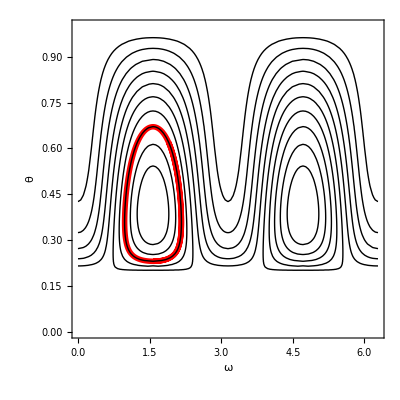

```mathematica
Show[
(* Plot result of integration *)
ParametricPlot[Evaluate[{g[t],Jz[t]/J[t]}/.soln],{t,0,1},AspectRatio->1,Frame->True,PlotStyle->Directive[Red,Thickness[0.01]]],

(* Contour plot showing level curves of the Hamiltonian *)
ContourPlot[Hexprn,{g,0,2Pi},{θ,0.2,1},Contours->10,ContourShading->None],

(* Plot options*)
PlotRange->{{0,2Pi},{0.0,1}},
Axes->False,
FrameLabel->{ω,θ},
FrameStyle->Directive[16,Black]
]
```

## surface of section with octupole term included

```mathematica
ϵ=0.01;
ℋ=Fqu+ϵ Foc;
equationsOfMotion = Thread[D[vars,t]==Jmatrix[2].Grad[ℋ,vars]];
initalCondtions=Thread[(vars/.t->0)=={g0,h0,√(1-e0^2),θ0 √(1-e0^2)}];
```

```mathematica
replaceRule=(initalCondtions/.Equal->Rule/.x_[0]:>x[t]);
```

```mathematica
ruleΩPi={g0->0,h0->Pi,e0->e,θ0->θ};
ruleΩ0={g0->0,h0->0,e0->e,θ0->θ};
exprnΩPi=(Fqu)+ϵ Foc/.replaceRule/.ruleΩPi;
exprnΩ0=(Fqu)+ϵ Foc/.replaceRule/.ruleΩ0;
```

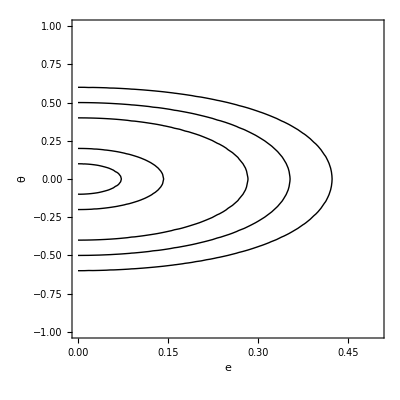

```mathematica
ContourPlot[exprnΩPi,{e,0,0.5},{θ,-1,1},Contours->{0.01,0.04,0.16,0.25,0.36},ContourShading->None,FrameLabel->{e,θ,"Constant Energy Contours"},FrameStyle->Directive[Black,18]]
```

Section for single trajectory

Integrate equations of motion and record points

```mathematica
Elevel = 0.16
```

0.16

```mathematica
initsrule=ruleΩPi/.First[FindInstance[exprnΩPi==Elevel&&e>0&&θ==0.3,{e,θ}]];
```

```mathematica
{soln,pts}=Reap@NDSolve[Evaluate[
Join[
equationsOfMotion,
initalCondtions,

{
(* Record ascending node (h) and cosi (Jz/J) every time the argument of perihelion passes g=π *)
WhenEvent[Mod[-g[t],2Pi]==Pi,Sow[{Mod[h[t],2Pi],Jz[t]/J[t]}]]
}
]//.initsrule],
{g,Jz[t],J[t]},{t,0,160}
];
```

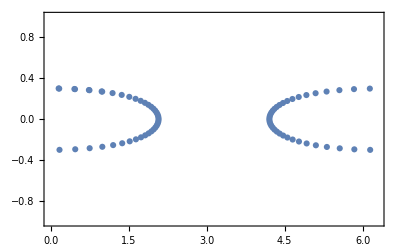

```mathematica
ListPlot[pts,PlotRange->{{0,2Pi},{-1,1}},Frame->True]
```

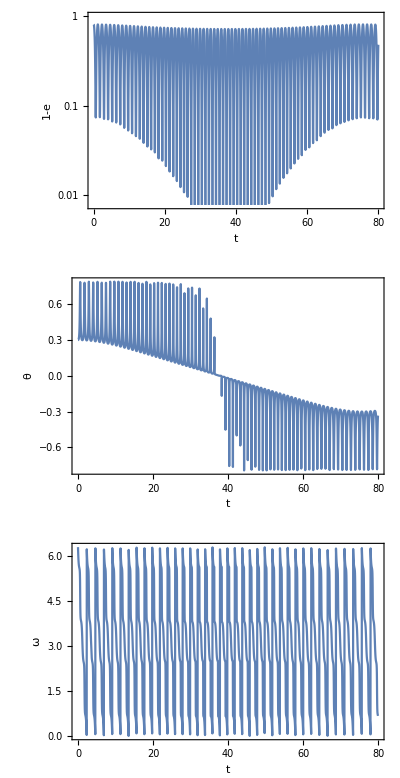

```mathematica
GraphicsColumn@{
LogPlot[1-√(1-J[t]^2)/.soln,{t,0,80},Frame->True,FrameLabel->{t,1-e}],
Plot[Jz[t]/J[t]/.soln,{t,0,80},Frame->True,FrameLabel->{t,θ}],
Plot[Mod[g[t]/.soln,2Pi],{t,0,80},Frame->True,FrameLabel->{t,ω}]
}
```

Show multiple trajectories

```mathematica
Elevel = 0.16;
```

```mathematica
allpts=Table[
initsrule=ruleΩPi/.First[FindInstance[exprnΩPi==Elevel&&e>0&&θ==θ0,{e,θ}]];
Last@Last@Reap@NDSolve[Evaluate[
Join[
equationsOfMotion,
initalCondtions,

{
(* Record ascending node (h) and cosi (Jz/J) every time the argument of perihelion passes g=π *)
WhenEvent[Mod[-g[t],2Pi]==Pi,Sow[{Mod[h[t],2Pi],Jz[t]/J[t]}]]
}
]//.initsrule],
{},{t,0,160}
]
,
{θ0,Most@Rest@Subdivide[0,√Elevel,8]}];
```

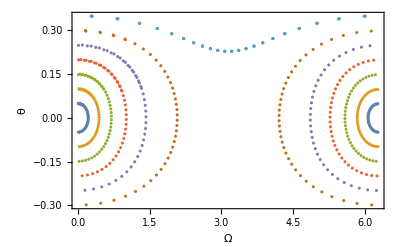

```mathematica
ListPlot[allpts,
Frame->True,FrameLabel->{Ω,θ},
FrameStyle->Directive[Black,18]]
```

# TOI-216

```mathematica
replaceRule=(initalCondtions/.Equal->Rule/.x_[0]:>x[t]);
```

## surface of section with octupole term included

```mathematica
Mstar = 1.1;
Rstar=1.1 Quantity["SolarRadius"]/Quantity["AstronomicalUnit"];
Pc=6.2679;
Pb=2093;
eb=0.64;
```

```mathematica
timeScale = (10*1*^-3)*(2Pi)/Pb
```

0.00511551

```mathematica
ab = Mstar^(1/3)(Pb/365.25)^(2/3);
ac = Mstar^(1/3)(Pc/365.25)^(2/3);
```

2319000/498659569

```mathematica
ϵ=(Pc/Pb)^(2/3)/(1-eb^2)eb;
```

```mathematica
ℋ=Fqu+ϵ*Foc;
```

```mathematica
equationsOfMotion = Thread[D[vars,t]==Jmatrix[2].Grad[ℋ,vars]];
initalCondtions=Thread[(vars/.t->0)=={g0,h0,√(1-e0^2),θ0 √(1-e0^2)}];
```

```mathematica
ruleΩPi={g0->0,h0->Pi,e0->e,θ0->θ};
ruleΩ0={g0->0,h0->0,e0->e,θ0->θ};
exprnΩPi=(Fqu)+ϵ Foc/.replaceRule/.ruleΩPi;
exprnΩ0=(Fqu)+ϵ Foc/.replaceRule/.ruleΩ0;
```

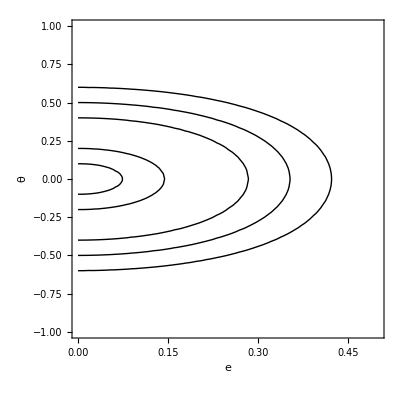

```mathematica
ContourPlot[exprnΩPi,{e,0,0.5},{θ,-1,1},Contours->{0.01,0.04,0.16,0.25,0.36},ContourShading->None,FrameLabel->{e,θ,"Constant Energy Contours"},FrameStyle->Directive[Black,18]]
```

```mathematica
Fqu/.{g[t]->0,h[t]->Pi,Jz[t]->θ0 √(1-e0^2),J[t]->√(1-e0^2)}/.e0->0
```

θ0^2

Section for single trajectory

Integrate equations of motion and record points

{g0→0,h0→π,e0→0.,θ0→Cos[20 °]}

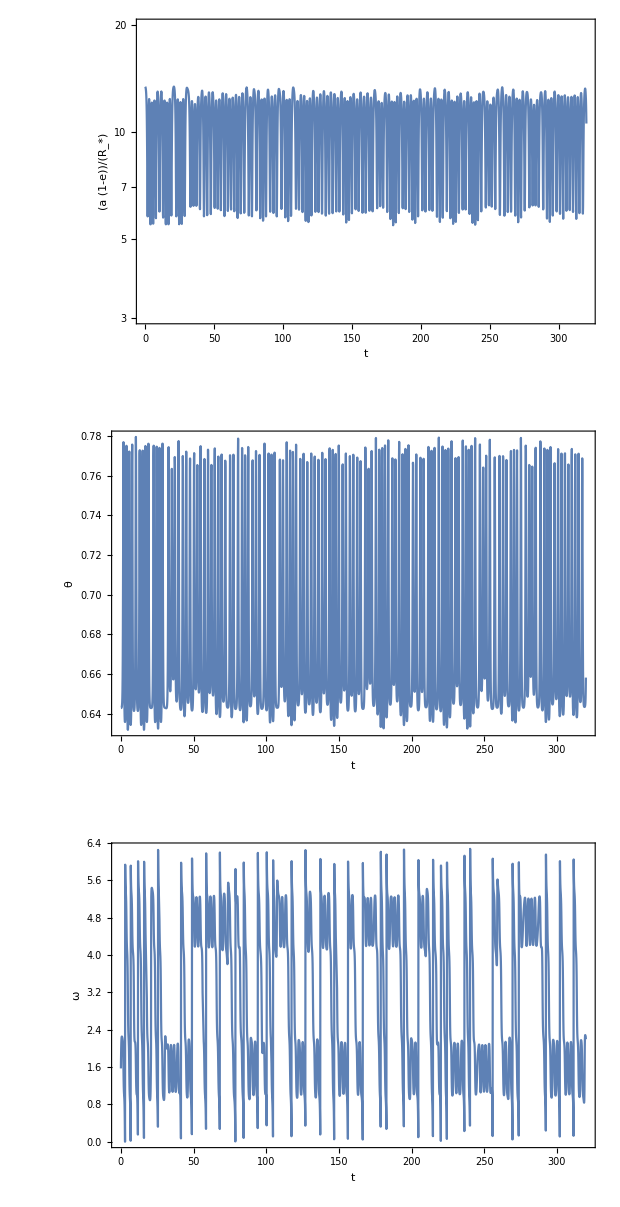

```mathematica
tstop=2 160;
initsrule={g0->Pi/2,h0->0,e0->0.001,θ0->Cos[50*Degree]};
{soln,pts}=Reap@NDSolve[Evaluate[
Join[
equationsOfMotion,
initalCondtions,

{
(* Record ascending node (h) and cosi (Jz/J) every time the argument of perihelion passes g=π *)
WhenEvent[Mod[-g[t],2Pi]==Pi,Sow[{Mod[h[t],2Pi],Jz[t]/J[t]}]]
}
]//.initsrule],
{g,Jz[t],J[t]},{t,0,tstop}
];
GraphicsColumn@{
LogPlot[(ac/Rstar)(1-√(1-J[t]^2))/.soln,{t,0,tstop},Frame->True,FrameLabel->{t,a(1-e)/SubStar[R]},PlotRange->{3,20}],
Plot[Jz[t]/J[t]/.soln,{t,0,tstop},Frame->True,FrameLabel->{t,θ}],
Plot[Mod[g[t]/.soln,2Pi],{t,0,tstop},Frame->True,FrameLabel->{t,ω}]
}
```

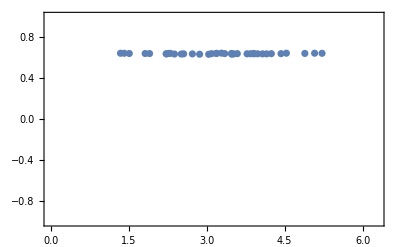

```mathematica
ListPlot[pts,PlotRange->{{0,2Pi},{-1,1}},Frame->True]
```

Show multiple trajectories

```mathematica
Elevel = 0.16;
```

```mathematica
allpts=Table[
initsrule=ruleΩPi/.First[FindInstance[exprnΩPi==Elevel&&e>0&&θ==θ0,{e,θ}]];
Last@Last@Reap@NDSolve[Evaluate[
Join[
equationsOfMotion,
initalCondtions,

{
(* Record ascending node (h) and cosi (Jz/J) every time the argument of perihelion passes g=π *)
WhenEvent[Mod[-g[t],2Pi]==Pi,Sow[{Mod[h[t],2Pi],Jz[t]/J[t]}]]
}
]//.initsrule],
{},{t,0,160}
]
,
{θ0,Most@Rest@Subdivide[0,√Elevel,8]}];
```

```mathematica
ListPlot[allpts,
Frame->True,FrameLabel->{Ω,θ},
FrameStyle->Directive[Black,18]]
```

-Graphics-

-1/2+5/2 Cos[2 g[t]]+J[t]^2/2-5/2 Cos[2 g[t]] J[t]^2-(3 Jz[t]^2)/2+5/2 Cos[2 g[t]] Jz[t]^2+(5 Jz[t]^2)/(2 J[t]^2)-(5 Cos[2 g[t]] Jz[t]^2)/(2 J[t]^2)+1/J[t]^3 0.000703805 (35/2 Cos[g[t]-h[t]] J[t]^3 √(1-J[t]^2)-175/2 Cos[3 g[t]-h[t]] J[t]^3 √(1-J[t]^2)+35/2 Cos[g[t]+h[t]] J[t]^3 √(1-J[t]^2)-175/2 Cos[3 g[t]+h[t]] J[t]^3 √(1-J[t]^2)-15/2 Cos[g[t]-h[t]] J[t]^5 √(1-J[t]^2)+175/2 Cos[3 g[t]-h[t]] J[t]^5 √(1-J[t]^2)-15/2 Cos[g[t]+h[t]] J[t]^5 √(1-J[t]^2)+175/2 Cos[3 g[t]+h[t]] J[t]^5 √(1-J[t]^2)-385/2 Cos[g[t]-h[t]] J[t]^2 √(1-J[t]^2) Jz[t]+175/2 Cos[3 g[t]-h[t]] J[t]^2 √(1-J[t]^2) Jz[t]+385/2 Cos[g[t]+h[t]] J[t]^2 √(1-J[t]^2) Jz[t]-175/2 Cos[3 g[t]+h[t]] J[t]^2 √(1-J[t]^2) Jz[t]+165/2 Cos[g[t]-h[t]] J[t]^4 √(1-J[t]^2) Jz[t]-175/2 Cos[3 g[t]-h[t]] J[t]^4 √(1-J[t]^2) Jz[t]-165/2 Cos[g[t]+h[t]] J[t]^4 √(1-J[t]^2) Jz[t]+175/2 Cos[3 g[t]+h[t]] J[t]^4 √(1-J[t]^2) Jz[t]-175/2 Cos[g[t]-h[t]] J[t] √(1-J[t]^2) Jz[t]^2+175/2 Cos[3 g[t]-h[t]] J[t] √(1-J[t]^2) Jz[t]^2-175/2 Cos[g[t]+h[t]] J[t] √(1-J[t]^2) Jz[t]^2+175/2 Cos[3 g[t]+h[t]] J[t] √(1-J[t]^2) Jz[t]^2+75/2 Cos[g[t]-h[t]] J[t]^3 √(1-J[t]^2) Jz[t]^2-175/2 Cos[3 g[t]-h[t]] J[t]^3 √(1-J[t]^2) Jz[t]^2+75/2 Cos[g[t]+h[t]] J[t]^3 √(1-J[t]^2) Jz[t]^2-175/2 Cos[3 g[t]+h[t]] J[t]^3 √(1-J[t]^2) Jz[t]^2+525/2 Cos[g[t]-h[t]] √(1-J[t]^2) Jz[t]^3-175/2 Cos[3 g[t]-h[t]] √(1-J[t]^2) Jz[t]^3-525/2 Cos[g[t]+h[t]] √(1-J[t]^2) Jz[t]^3+175/2 Cos[3 g[t]+h[t]] √(1-J[t]^2) Jz[t]^3-225/2 Cos[g[t]-h[t]] J[t]^2 √(1-J[t]^2) Jz[t]^3+175/2 Cos[3 g[t]-h[t]] J[t]^2 √(1-J[t]^2) Jz[t]^3+225/2 Cos[g[t]+h[t]] J[t]^2 √(1-J[t]^2) Jz[t]^3-175/2 Cos[3 g[t]+h[t]] J[t]^2 √(1-J[t]^2) Jz[t]^3)

```mathematica
initalCondtions=Thread[(vars/.t->0)=={g0,h0,√(1-e0^2),θ0 √(1-e0^2)}];
initsrule={g0->Pi/2,h0->0,e0->0.5,θ0->0.2/(√(1-e0^2))};
```

```mathematica
GraphicsColumn@{
LogPlot[1-√(1-J[t]^2)/.soln,{t,0,80},Frame->True,FrameLabel->{t,1-e}],
Plot[Jz[t]/J[t]/.soln,{t,0,80},Frame->True,FrameLabel->{t,θ}],
Plot[Mod[g[t]/.soln,2Pi],{t,0,80},Frame->True,FrameLabel->{t,ω}]
}
```